```mathematica
(*Type I boundary arc for Θ4*)
```

```mathematica
Solve[t^4-α*t-(1-α)==0,t]
```

{{t→1},{t→-1/3-(2 2^(1/3))/(3 (-20+27 α+3 √3 √(16-40 α+27 α^2))^(1/3))+((-20+27 α+3 √3 √(16-40 α+27 α^2))^(1/3))/(3 2^(1/3))},{t→-1/3+(2^(1/3) (1+ⅈ √3))/(3 (-20+27 α+3 √3 √(16-40 α+27 α^2))^(1/3))-((1-ⅈ √3) (-20+27 α+3 √3 √(16-40 α+27 α^2))^(1/3))/(6 2^(1/3))},{t→-1/3+(2^(1/3) (1-ⅈ √3))/(3 (-20+27 α+3 √3 √(16-40 α+27 α^2))^(1/3))-((1+ⅈ √3) (-20+27 α+3 √3 √(16-40 α+27 α^2))^(1/3))/(6 2^(1/3))}}

```mathematica
(*Plotting the curved arcs toghether with the unit circle*)
```

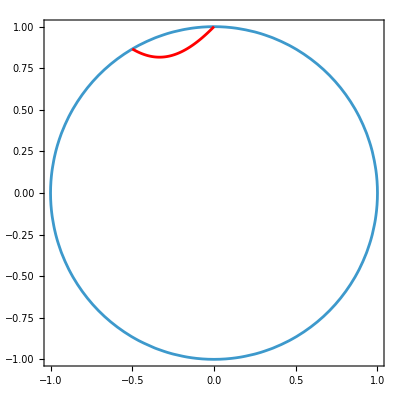

```mathematica
Show[
	 ContourPlot[
	   x^2+y^2==1,
	   {x,-1,1},
	   {y,-1,1},
	   PlotRange->{{-1,1},{-1,1}}
	 ],
	 ParametricPlot[
	 {
	   Re[-1/3+(2^(1/3) (1+ⅈ √3))/(3 (-20+27 α+3 √3 √(16-40 α+27 α^2))^(1/3))-((1-ⅈ √3) (-20+27 α+3 √3 √(16-40 α+27 α^2))^(1/3))/(6 2^(1/3))],
	   Im[-1/3+(2^(1/3) (1+ⅈ √3))/(3 (-20+27 α+3 √3 √(16-40 α+27 α^2))^(1/3))-((1-ⅈ √3) (-20+27 α+3 √3 √(16-40 α+27 α^2))^(1/3))/(6 2^(1/3))]},
	 {α,0,1},
	   PlotRange->{{-1,1},{-1,1}},
	   AxesLabel->{"Re","Im"},
	   PlotStyle->Red
	 ]
]
```

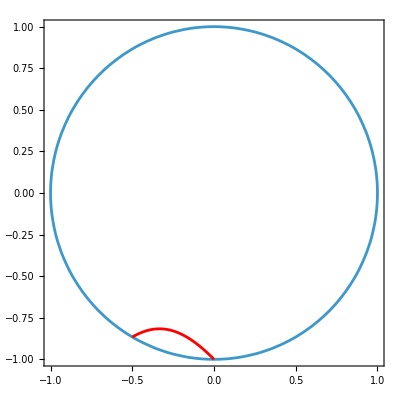

```mathematica
Show[
	 ContourPlot[
	   x^2+y^2==1,
	   {x,-1,1},
	   {y,-1,1},
	   PlotRange->{{-1,1},{-1,1}}
	 ],
	 ParametricPlot[
	 {
	   Re[-1/3+(2^(1/3) (1-ⅈ √3))/(3 (-20+27 α+3 √3 √(16-40 α+27 α^2))^(1/3))-((1+ⅈ √3) (-20+27 α+3 √3 √(16-40 α+27 α^2))^(1/3))/(6 2^(1/3))],
	   Im[-1/3+(2^(1/3) (1-ⅈ √3))/(3 (-20+27 α+3 √3 √(16-40 α+27 α^2))^(1/3))-((1+ⅈ √3) (-20+27 α+3 √3 √(16-40 α+27 α^2))^(1/3))/(6 2^(1/3))]},
	 {α,0,1},
	   PlotRange->{{-1,1},{-1,1}},
	   AxesLabel->{"Re","Im"},
	   PlotStyle->Red
	 ]
]
```

```mathematica
With[{α=0}, NSolve[t==-1/3+(2^(1/3) (1+ⅈ √3))/(3 (-20+27 α+3 √3 √(16-40 α+27 α^2))^(1/3))-((1-ⅈ √3) (-20+27 α+3 √3 √(16-40 α+27 α^2))^(1/3))/(6 2^(1/3))]]
```

{{t→-1.249×10^-16+1. ⅈ}}

```mathematica
With[{α=1}, Solve[t==-1/3+(2^(1/3) (1+ⅈ √3))/(3 (-20+27 α+3 √3 √(16-40 α+27 α^2))^(1/3))-((1-ⅈ √3) (-20+27 α+3 √3 √(16-40 α+27 α^2))^(1/3))/(6 2^(1/3))]]
```

{{t→1/2 (-1+ⅈ √3)}}